```mathematica
n=1000; m=10000;
```

```mathematica
(*En este codigo, se leen los datos exportados, se hace el grafo t, y la contraparte aleatoria r. Se analizan la distribucion de grados (comun a ambos), el numero de CCs y el tamaño de las mismas. Posteriormente se corrige el hecho de los nodos sin vecinos, al añadirle {1} por cada nodo faltante en las listas de CC, y agregarle un {0} en la lista de vertex degree. Posteriormente se exporta a 'lvd'  (list of vertex degree) la lista de valores que tiene la red para los grados de los nodos, lo mismo se hace para lncct 'list of number of Connected Components' y lscct 'list of sizes of connected components'. Se generan las contrapartes aleatorias y se analizan sus propiedades, diferenciandose de las redes de parentesco acá en que sus elementos terminan en -r en vez de -t por ejemplo lsccr, lnccr. *)
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};lgcct={}; lmcct={}; lassortt={}; lgccr={}; lmccr={}; lassortr={};Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n1490.txt"]]]; While[spression≠ {0,0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n1490.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], v=VertexDegree[Graph[t]],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]],Do[{ cct=Join[cct, {1}], ccr=Join[ccr, {1}],v=Join[v, {0}]}, x], ncct=Length[cct], nccr=Length[ccr], lvd=Join[lvd, v],  lncct=Join[lncct, {ncct}] , lnccr=Join[lnccr, {nccr}], lscct=Join[lscct, Table[Length[cct[[i]]], {i, 1, Length[cct]}]],lsccr=Join[lsccr, Table[Length[ccr[[i]]], {i, 1, Length[ccr]}]], lgcct=Join[lgcct, {GlobalClusteringCoefficient[Graph[t]]}], lgccr=Join[lgccr, {GlobalClusteringCoefficient[Graph[r]]}] , lmcct=Join[lmcct, {MeanClusteringCoefficient[Graph[t]]}], lmccr=Join[lmccr, {MeanClusteringCoefficient[Graph[r]]}] , lassortt=Join[lassortt, {GraphAssortativity[Graph[t]]}], lassortr=Join[lassortr, {GraphAssortativity[Graph[r]]}]} , m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Analisis de Vertex Degree*)
```

```mathematica
blvd=HistogramList[lvd]; hlvd=Table[{Floor[(blvd[[1, i]]+blvd[[1, i+1]])/2],blvd[[2, i]]/(Length[lvd]*(blvd[[1,2]]-blvd[[1,1]]))}, {i, 1, Length[blvd[[2]]]}]; TableForm[N[hlvd]]
```

```mathematica
Print[Mean[N[lvd]]]; Print[StandardDeviation[N[lvd]]];
```

2.01336

1.41712

```mathematica
(*Analisis de Number of Connected Components*)
```

```mathematica
blncct=HistogramList[lncct]; hlncct=Table[{Floor[(blncct[[1, i]]+blncct[[1, i+1]])/2],blncct[[2, i]]/(Length[lncct]*(blncct[[1,2]]-blncct[[1,1]]))}, {i, 1, Length[blncct[[2]]]}]; TableForm[N[hlncct]]
```

```mathematica
blnccr=HistogramList[lnccr]; hlnccr=Table[{Floor[(blnccr[[1, i]]+blnccr[[1, i+1]])/2],blnccr[[2, i]]/(Length[lnccr]*(blnccr[[1,2]]-blnccr[[1,1]]))}, {i, 1, Length[blnccr[[2]]]}]; TableForm[N[hlnccr]]
```

```mathematica
Print[Mean[N[lncct]]]; Print[StandardDeviation[N[lncct]]]; Print[Mean[N[lnccr]]]; Print[StandardDeviation[N[lnccr]]];
```

242.667

15.1886

164.991

12.2125

```mathematica
(*Analisis de Size of Connected Components*)
```

```mathematica
w=(Max[lscct]-Min[lscct])/Sqrt[Length[lscct]]; blscct=HistogramList[lscct, {Min[lscct], Max[lscct], w}]; hlscct=Table[{Floor[blscct[[1, i]]], blscct[[2, i]]/(Length[lscct]*w)}, {i, 1, Length[blscct[[2]]]}];TableForm[N[hlscct]]
```

```mathematica
w=(Max[lsccr]-Min[lsccr])/Sqrt[Length[lsccr]]; blsccr=HistogramList[lsccr, {Min[lsccr], Max[lsccr], w}]; hlsccr=Table[{Floor[blsccr[[1, i]]], blsccr[[2, i]]/(Length[lsccr]*w)}, {i, 1, Length[blsccr[[2]]]}];TableForm[N[hlsccr]]
```

```mathematica
(*Analisis de Global and Mean Clusstering Coefficients*)
```

```mathematica
Print[Mean[N[lgcct]]];Print[ StandardDeviation[N[lgcct]]];Print[Mean[N[lgccr]]];Print[ StandardDeviation[N[lgccr]]]
```

0.444259

0.0215909

0.00348285

0.00230325

```mathematica
Print[Mean[N[lmcct]]];Print[ StandardDeviation[N[lmcct]]];Print[Mean[N[lmccr]]];Print[ StandardDeviation[N[lmccr]]]
```

0.309319

0.0193132

0.0023027

0.00182613

```mathematica
(*Analisis de Assortativity*)
```

```mathematica
Print[Mean[N[lassortt]]];Print[ StandardDeviation[N[lassortt]]];Print[Mean[N[lassortr]]];Print[ StandardDeviation[N[lassortr]]]
```

0.435165

0.0493931

0.0583911

0.032875

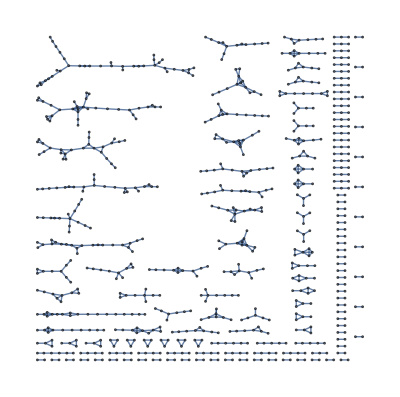

```mathematica
Graph[t]
```